## Initialise

```mathematica
PrependTo[$Path,"/Users/hhakula/Projects/Text/hnv/hpFEM"];
```

```mathematica
<<VSHP2D`
```

```mathematica
<<VSHP2D`Curve`
```

Curve

```mathematica
<<VSHP2D`SimplexComplex`
```

SC

```mathematica
<<VSHP2D`Mesh`
```

Mesh

## Auxiliary

```mathematica
ViewInstance[acase_Integer,tcase_Integer]:=Block[{t=ts[[tcase]],a=as[[acase]],r1=r1s[[tcase,acase]],s=ss[[tcase,acase]],r2=r2s[[tcase,acase]]},
left=Circle[{-t,0},r1];
right=Circle[{t,0},r1];
top=Circle[{0,s},r2];
bottom=Circle[{0,-s},r2];
Graphics[{left,right,top,bottom}]
]
```

```mathematica
SimplexComplexPartition[s_SimplexComplex2D]:=Block[{curves=s["Curves"],ncurves,cc},
ncurves=Flatten[MakeCurveSlices[#,{-1,0,1}]&/@Values@curves];
cc=Through[ncurves[-1]];
MakeSimplexComplex[{{1,2,9,8},{2,3,4,9},{4,5,6,9},{6,7,8,9}},Append[cc,{0,0}],"Curves"->AssociationThread[Partition[Range[8],2,1,{1,1}],ncurves]]
]
```

## Setup

```mathematica
as=Table[Pi/k,{k,4,8}]
```

{π/4,π/5,π/6,π/7,π/8}

```mathematica
ts=FullSimplify@Table[1+(1/5)j((1/Cos[as[[j]]])-1),{j,5}]
```

{1/5 (4+√2),1/5+2/(√5),2/5 (1+√3),1/5 (1+4 Sec[π/7]),Sec[π/8]}

```mathematica
r1s=MapThread[FullSimplify@EuclideanDistance[#1,ReIm[Exp[I(Pi-#2)]]]&,{Thread[List[-ts,0]],as}]
```

{1/5 √(33-12 √2),1/5 √(1/2 (37-7 √5)),1/5 √(11-2 √3),√((-1/5+Cos[π/7]-4/5 Sec[π/7])^2+Sin[π/7]^2),Tan[π/8]}

```mathematica
sd=Monitor[Table[
line=InterpolatingPolynomial[{{-t,0},ReIm[Exp[I(Pi-a)]]},x];
s=line/.x->0;
r1=EuclideanDistance[{-t,0},ReIm[Exp[I(Pi-a)]]];
r2=EuclideanDistance[{0,s},ReIm[Exp[I(Pi-a)]]];
{s,r1,r2},{t,ts},{a,as}],{t,a}];
```

```mathematica
ss=sd[[All,All,1]];
r1s=sd[[All,All,2]];
r2s=sd[[All,All,3]];
```

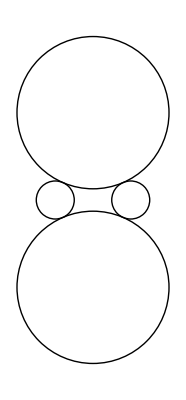

```mathematica
ViewInstance[3,5]
```

## Unified

```mathematica
OneCase[tcase_Integer,acase_Integer]:=Block[{},
lc=MakeCircleArch[{{-ts[[tcase]],0},r1s[[tcase,acase]]},{ReIm[Exp[I(Pi+as[[acase]])]],ReIm[Exp[I(Pi-as[[acase]])]]}];rc=MakeCircleArch[{{ts[[tcase]],0},r1s[[tcase,acase]]},{ReIm[Exp[I(as[[acase]])]],ReIm[Exp[I(-as[[acase]])]]}];tc=MakeCircleArch[{{0,ss[[tcase,acase]]},r2s[[tcase,acase]]},{ReIm[Exp[I(Pi-as[[acase]])]],ReIm[Exp[I(as[[acase]])]]}];bc=MakeCircleArch[{{0,-ss[[tcase,acase]]},r2s[[tcase,acase]]},{ReIm[Exp[I(-as[[acase]])]],ReIm[Exp[I(Pi+as[[acase]])]]}];
curves=MakeReverseCopy/@{bc,rc,tc,lc};s=MakeSimplexComplex[{{1,2,3,4}},Through[curves[-1]],"Curves"->AssociationThread[Partition[Range[4],2,1,{1,1}],curves]];
ns=SimplexComplexPartition[s];
pm=ConvertToPMesh[ns];
sings=s["Coordinates"];
marked=MarkBoundary[
pm["Boundaries"][[1]],
<|
"A"->sings[[1]],
"B"->sings[[2]],
"C"->sings[[3]],
"D"->sings[[4]]
|>];
p=20;
o=MakePOrdering[pm, "PolynomialDegree"->p];varForm=Function[qn,{List@{0,0,0,0,1,0,0,0,1},1}];A0=AssembleSystem[o,pm["Elements"], varForm, "QuadratureOffset"->5];A0=(A0+Transpose[A0])/2;
d1=Composition[Union,Flatten][Steering[o,"Nodes"->#["Nodes"]]&/@marked["A"]];
r =ActiveDof[o, marked, <|
"A" -> {1}, 
          "C" -> {1}
|>];
db=ConstantArray[0,o["SystemSize"]];
db[[d1]]=1;
rhs=-A0.db;
sol=LinearSolve[A0[[r,r]],rhs[[r]]];
db[[r]]=sol;
R1=db.A0.db;
d1=Composition[Union,Flatten][Steering[o,"Nodes"->#["Nodes"]]&/@marked["B"]];
r =ActiveDof[o, marked, <|
"B" -> {1}, 
          "D" -> {1}
|>];
db=ConstantArray[0,o["SystemSize"]];
db[[d1]]=1;
rhs=-A0.db;
sol=LinearSolve[A0[[r,r]],rhs[[r]]];
db[[r]]=sol;
R2=db.A0.db;
{R1,R2,Abs[1-R1 R2]}
]
```

```mathematica
vals=Monitor[Table[OneCase[i,j],{i,5},{j,5}],{i,j}]
```

{{{0.605343,1.65196,2.10232×10^-11},{1.10582,0.904303,3.32883×10^-11},{1.65941,0.602623,1.34633×10^-10},{2.29247,0.436211,1.89246×10^-10},{3.04399,0.328516,9.79478×10^-10}},{{0.619813,1.61339,2.06781×10^-11},{1.13467,0.881314,3.58218×10^-11},{1.71368,0.583541,1.38465×10^-10},{2.39061,0.418304,1.98377×10^-10},{3.21882,0.310673,1.03224×10^-9}},{{0.617809,1.61862,2.07281×10^-11},{1.13065,0.884445,3.54663×10^-11},{1.70607,0.586144,1.37941×10^-10},{2.37671,0.42075,1.97114×10^-10},{3.19372,0.313115,1.02526×10^-9}},{{0.611708,1.63477,2.08737×10^-11},{1.11847,0.894082,3.43925×10^-11},{1.68308,0.594147,1.36337×10^-10},{2.33501,0.428264,1.93261×10^-10},{3.11909,0.320606,1.00334×10^-9}},{{0.604779,1.6535,2.10341×10^-11},{1.10471,0.905217,3.31934×10^-11},{1.65733,0.60338,1.3448×10^-10},{2.28875,0.43692,1.88889×10^-10},{3.03747,0.329221,9.7732×10^-10}}}

```mathematica
Flatten@Table[<|"t"->i,"a"->j,"R1"->ScientificForm[vals[[i,j,1]],16],"R2"->ScientificForm[vals[[i,j,2]],16],"E"->Floor@Abs@Log[10,vals[[i,j,3]]]|>,{i,5},{j,5}]
```

{<|t→1,a→1,R1→6.053428462478877×10^-1,R2→1.651956418118012,E→10|>,<|t→1,a→2,R1→1.105823804450106,R2→9.04303195508221×10^-1,E→10|>,<|t→1,a→3,R1→1.659413257938523,R2→6.02622641075512×10^-1,E→9|>,<|t→1,a→4,R1→2.292470464019097,R2→4.362106364659864×10^-1,E→9|>,<|t→1,a→5,R1→3.043991439042823,R2→3.285160359366603×10^-1,E→9|>,<|t→2,a→1,R1→6.198133006025127×10^-1,R2→1.613389062558985,E→10|>,<|t→2,a→2,R1→1.134669460541902,R2→8.81313928690948×10^-1,E→10|>,<|t→2,a→3,R1→1.713675635567149,R2→5.835410035502492×10^-1,E→9|>,<|t→2,a→4,R1→2.390608573773721,R2→4.1830352788362×10^-1,E→9|>,<|t→2,a→5,R1→3.218817156719697,R2→3.106731300175314×10^-1,E→8|>,<|t→3,a→1,R1→6.178094632053507×10^-1,R2→1.618622017915486,E→10|>,<|t→3,a→2,R1→1.130652472644239,R2→8.84445065331863×10^-1,E→10|>,<|t→3,a→3,R1→1.706065071323858,R2→5.861441142816255×10^-1,E→9|>,<|t→3,a→4,R1→2.376709968794099,R2→4.207496974081766×10^-1,E→9|>,<|t→3,a→5,R1→3.193717049556967,R2→3.13114776765832×10^-1,E→8|>,<|t→4,a→1,R1→6.117081757685474×10^-1,R2→1.634766445232612,E→10|>,<|t→4,a→2,R1→1.118466179620068,R2→8.94081571938172×10^-1,E→10|>,<|t→4,a→3,R1→1.6830845048837,R2→5.941472322005818×10^-1,E→9|>,<|t→4,a→4,R1→2.335009735204089,R2→4.282637391684609×10^-1,E→9|>,<|t→4,a→5,R1→3.119089883734634,R2→3.206063429650175×10^-1,E→8|>,<|t→5,a→1,R1→6.047789617672523×10^-1,R2→1.653496671079444,E→10|>,<|t→5,a→2,R1→1.104707352332473,R2→9.05217112859618×10^-1,E→10|>,<|t→5,a→3,R1→1.657331065357307,R2→6.033797477385049×10^-1,E→9|>,<|t→5,a→4,R1→2.288748449339525,R2→4.369200121041978×10^-1,E→9|>,<|t→5,a→5,R1→3.037469189026014,R2→3.292214467854327×10^-1,E→9|>}